## 1. Optimal conditions and amplitude (*{R1^2->R1R1}*)

```mathematica
OptimalConditionI[g10_,h_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionII[g10_,KK_]=ϕ1^2-4*ϕ0*ϕ2;


OptimalConditionIII[g10_,phif_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionIV[g10_,cf_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionV[g10_,beta_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVI[g10_,lamdaf_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVII[g10_,g30_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVIII[g10_,c0_]= ϕ1^2-4*ϕ0*ϕ2;


OptimalCondition=ϕ1^2-4*ϕ0*ϕ2;
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

amplitude=Amplitude/.{R1^2->R1R1};
```

## 2. parametric study for skin matrix

### 2.1 Relations of h and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;
cf=100;phif=0.05;lamdaf=0.885;g12=1;
beta=Pi/4;

hmin=10^-3;
hmax=5*10^-2;
samplePoints=Subdivide[hmin,hmax,49];
datahtestXY=Table[{0,0,0,0,0},{h,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.12;
ninit=2.5;

For[i=Length[samplePoints],i>=1,i--,h=samplePoints[[i]];
1/□(sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at h = ",h];
Continue[];];
g10=g10/. sol;)
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datahtestXY[[k]]={h,n,g10,Sqrt[R12]};
Print[{h,n,g10,Sqrt[R12]}];
k++;]


vdatahtestXY=Select[datahtestXY,#[[2]]>0&&#[[3]]>0&];
Maxg10htestXY=Max[vdatahtestXY[[All,3]]]
```

{1/20,2.4271,1.15892,0.468043}

{49/1000,2.46434,1.15855,0.461168}

{6/125,2.50293,1.15818,0.454259}

{47/1000,2.54295,1.15781,0.447316}

{23/500,2.58449,1.15743,0.440337}

{9/200,2.62764,1.15705,0.433321}

{11/250,2.6725,1.15667,0.426267}

{43/1000,2.71918,1.15628,0.419173}

{21/500,2.76779,1.15589,0.412038}

{41/1000,2.81847,1.15549,0.404859}

{1/25,2.87136,1.15509,0.397637}

{39/1000,2.92661,1.15468,0.390368}

{19/500,2.9844,1.15427,0.383051}

{37/1000,3.0449,1.15386,0.375684}

{9/250,3.10834,1.15344,0.368265}

{7/200,3.17493,1.15301,0.360792}

{17/500,3.24493,1.15258,0.353262}

{33/1000,3.31863,1.15214,0.345673}

{4/125,3.39635,1.15169,0.338023}

{31/1000,3.47842,1.15124,0.330308}

{3/100,3.56526,1.15078,0.322526}

{29/1000,3.65732,1.15031,0.314674}

{7/250,3.7551,1.14984,0.306747}

{27/1000,3.85918,1.14936,0.298743}

{13/500,3.97023,1.14887,0.290656}

{1/40,4.08902,1.14837,0.282484}

{3/125,4.21641,1.14786,0.27422}

{23/1000,4.35343,1.14734,0.265861}

{11/500,4.50129,1.14681,0.2574}

{21/1000,4.6614,1.14626,0.24883}

{1/50,4.83541,1.14571,0.240146}

{19/1000,5.02535,1.14514,0.231339}

{9/500,5.23361,1.14456,0.222401}

{17/1000,5.46315,1.14396,0.213322}

{2/125,5.7176,1.14334,0.204091}

{3/200,6.00147,1.14271,0.194697}

{7/500,6.32051,1.14205,0.185125}

{13/1000,6.68208,1.14137,0.175358}

{3/250,7.09584,1.14067,0.165378}

{11/1000,7.57468,1.13993,0.155162}

{1/100,8.1363,1.13916,0.144682}

{9/1000,8.80565,1.13836,0.133906}

{1/125,9.61925,1.13751,0.122792}

{7/1000,10.6328,1.1366,0.111287}

{3/500,11.9363,1.13563,0.0993202}

{1/200,13.6856,1.13457,0.086795}

{1/250,16.1789,1.13341,0.0735698}

{3/1000,20.0748,1.13209,0.0594201}

{1/500,27.2088,1.13052,0.0439401}

❌ FindRoot failed at h = 1/1000

1.15892

#### Graph

{1/20,1.15892,2.4271,0.468043,0.0468043}

{49/1000,1.15855,2.46434,0.461168,0.0469524}

{6/125,1.15818,2.50293,0.454259,0.0470653}

{47/1000,1.15781,2.54295,0.447316,0.0471437}

{23/500,1.15743,2.58449,0.440337,0.047188}

{9/200,1.15705,2.62764,0.433321,0.0471988}

{11/250,1.15667,2.6725,0.426267,0.0471762}

{43/1000,1.15628,2.71918,0.419173,0.0471207}

{21/500,1.15589,2.76779,0.412038,0.0470325}

{41/1000,1.15549,2.81847,0.404859,0.0469119}

{1/25,1.15509,2.87136,0.397637,0.0467588}

{39/1000,1.15468,2.92661,0.390368,0.0465735}

{19/500,1.15427,2.9844,0.383051,0.0463558}

{37/1000,1.15386,3.0449,0.375684,0.0461059}

{9/250,1.15344,3.10834,0.368265,0.0458236}

{7/200,1.15301,3.17493,0.360792,0.0455088}

{17/500,1.15258,3.24493,0.353262,0.0451613}

{33/1000,1.15214,3.31863,0.345673,0.0447807}

{4/125,1.15169,3.39635,0.338023,0.0443669}

{31/1000,1.15124,3.47842,0.330308,0.0439194}

{3/100,1.15078,3.56526,0.322526,0.0434378}

{29/1000,1.15031,3.65732,0.314674,0.0429215}

{7/250,1.14984,3.7551,0.306747,0.0423699}

{27/1000,1.14936,3.85918,0.298743,0.0417824}

{13/500,1.14887,3.97023,0.290656,0.0411583}

{1/40,1.14837,4.08902,0.282484,0.0404965}

{3/125,1.14786,4.21641,0.27422,0.0397962}

{23/1000,1.14734,4.35343,0.265861,0.0390562}

{11/500,1.14681,4.50129,0.2574,0.0382753}

{21/1000,1.14626,4.6614,0.24883,0.0374521}

{1/50,1.14571,4.83541,0.240146,0.0365851}

{19/1000,1.14514,5.02535,0.231339,0.0356724}

{9/500,1.14456,5.23361,0.222401,0.0347121}

{17/1000,1.14396,5.46315,0.213322,0.0337019}

{2/125,1.14334,5.7176,0.204091,0.0326393}

{3/200,1.14271,6.00147,0.194697,0.0315212}

{7/500,1.14205,6.32051,0.185125,0.0303443}

{13/1000,1.14137,6.68208,0.175358,0.0291045}

{3/250,1.14067,7.09584,0.165378,0.0277972}

{11/1000,1.13993,7.57468,0.155162,0.0264169}

{1/100,1.13916,8.1363,0.144682,0.0249568}

{9/1000,1.13836,8.80565,0.133906,0.023409}

{1/125,1.13751,9.61925,0.122792,0.0217631}

{7/1000,1.1366,10.6328,0.111287,0.0200062}

{3/500,1.13563,11.9363,0.0993202,0.0181214}

{1/200,1.13457,13.6856,0.086795,0.0160852}

{1/250,1.13341,16.1789,0.0735698,0.0138637}

{3/1000,1.13209,20.0748,0.0594201,0.0114036}

{1/500,1.13052,27.2088,0.0439401,0.00860996}

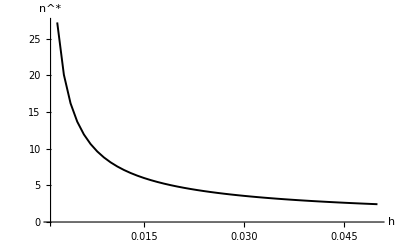

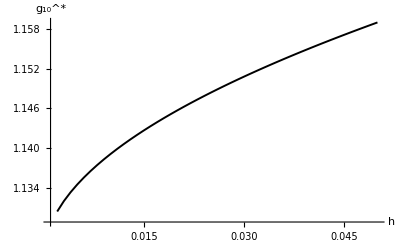

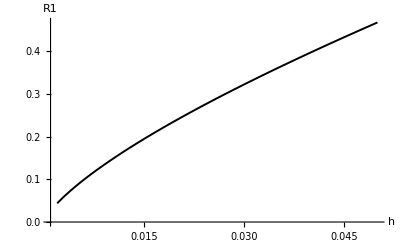

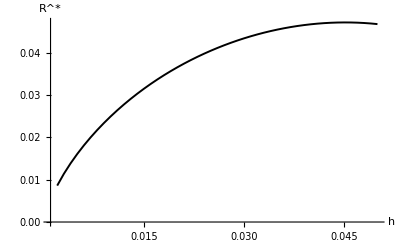

VRdatahtestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdatahtestXY.xlsx

```mathematica
g1externalh=1.15892+0.01;


RdatahtestXY=Table[{0,0,0,0,0},{Length[vdatahtestXY]}];
For[i=1,i<=Length[vdatahtestXY],i++,Module[{h,g10,n,Rstar},{h,n,g10}=vdatahtestXY[[i,{1,2,3}]];
R1=vdatahtestXY[[i,4]];
Rstar=Sqrt[g1externalh-g10]*R1;
RdatahtestXY[[i]]={h,g10,n,R1,Rstar};
Print[{h,g10,n,R1,Rstar}];]];

VRdatahtestXY=Select[RdatahtestXY,#[[2]]>0&];
testhnXY=ListPlot[VRdatahtestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testhg10XY=ListPlot[VRdatahtestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhR1XY=ListLinePlot[VRdatahtestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhRXY=ListLinePlot[VRdatahtestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatahtestXY.xlsx",VRdatahtestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatahtestXY.xlsx",VRdatahtestXY]
```

### 2.2 Relations of g30 and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;h=1/75;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;g12=1;


samplePoints=Subdivide[0.5,1.5,49];
datag30testXY=Table[{0,0,0,0,0},{ g30,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.14;
ninit=5;

For[i=Length[samplePoints],i>=1,i--, g30=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  g30 = ", g30];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datag30testXY[[k]]={ g30,n,g10,Sqrt[R12]};
Print[{ g30,n,g10,R12}];
k++;]


vdatag30testXY=Select[datag30testXY,#[[2]]>0&&#[[3]]>0&];
Maxg10g30testXY=Max[vdatag30testXY[[All,3]]]
```

{1.5,4.83541,1.14571,0.05767}

{1.47959,4.88543,1.14556,0.0565307}

{1.45918,4.93666,1.1454,0.0553984}

{1.43878,4.98916,1.14525,0.0542732}

{1.41837,5.04299,1.14509,0.0531551}

{1.39796,5.09818,1.14493,0.0520441}

{1.37755,5.1548,1.14477,0.0509405}

{1.35714,5.21291,1.14461,0.0498441}

{1.33673,5.27257,1.14445,0.048755}

{1.31633,5.33384,1.14429,0.0476734}

{1.29592,5.3968,1.14413,0.0465993}

{1.27551,5.46151,1.14396,0.0455328}

{1.2551,5.52806,1.1438,0.0444738}

{1.23469,5.59653,1.14363,0.0434226}

{1.21429,5.66701,1.14346,0.0423791}

{1.19388,5.7396,1.14329,0.0413434}

{1.17347,5.81438,1.14312,0.0403156}

{1.15306,5.89148,1.14295,0.0392959}

{1.13265,5.971,1.14277,0.0382842}

{1.11224,6.05307,1.1426,0.0372807}

{1.09184,6.13781,1.14242,0.0362854}

{1.07143,6.22537,1.14224,0.0352984}

{1.05102,6.3159,1.14206,0.0343198}

{1.03061,6.40956,1.14188,0.0333498}

{1.0102,6.50652,1.14169,0.0323883}

❌ FindRoot failed at  g30 = 0.989796

{0.969388,6.7111,1.14132,0.0304917}

{0.94898,6.81914,1.14113,0.0295567}

{0.928571,6.93133,1.14094,0.0286308}

{0.908163,7.04791,1.14074,0.027714}

{0.887755,7.16917,1.14055,0.0268064}

{0.867347,7.29541,1.14035,0.0259083}

❌ FindRoot failed at  g30 = 0.846939

{0.826531,7.56415,1.13995,0.0241407}

❌ FindRoot failed at  g30 = 0.806122

{0.785714,7.85717,1.13953,0.0224122}

{0.765306,8.01388,1.13932,0.0215631}

{0.744898,8.17808,1.13911,0.0207242}

{0.72449,8.35035,1.13889,0.0198957}

{0.704082,8.53131,1.13868,0.0190778}

{0.683673,8.7217,1.13845,0.0182706}

{0.663265,8.92229,1.13823,0.0174744}

{0.642857,9.13398,1.138,0.0166893}

{0.622449,9.35777,1.13777,0.0159156}

{0.602041,9.59477,1.13753,0.0151535}

{0.581633,9.84626,1.13729,0.0144031}

{0.561224,10.1137,1.13705,0.0136648}

{0.540816,10.3987,1.1368,0.0129388}

{0.520408,10.7031,1.13654,0.0122254}

{0.5,11.0292,1.13628,0.0115247}

1.14571

#### Graph

{1.5,1.14571,4.83541,0.240146,0.0240146}

{1.47959,1.14556,4.88543,0.237762,0.0239578}

{1.45918,1.1454,4.93666,0.235369,0.0238962}

{1.43878,1.14525,4.98916,0.232966,0.0238299}

{1.41837,1.14509,5.04299,0.230554,0.0237588}

{1.39796,1.14493,5.09818,0.228132,0.0236829}

{1.37755,1.14477,5.1548,0.2257,0.0236023}

{1.35714,1.14461,5.21291,0.223258,0.0235169}

{1.33673,1.14445,5.27257,0.220805,0.0234266}

{1.31633,1.14429,5.33384,0.218342,0.0233315}

{1.29592,1.14413,5.3968,0.215869,0.0232316}

{1.27551,1.14396,5.46151,0.213384,0.0231268}

{1.2551,1.1438,5.52806,0.210888,0.0230172}

{1.23469,1.14363,5.59653,0.208381,0.0229026}

{1.21429,1.14346,5.66701,0.205862,0.022783}

{1.19388,1.14329,5.7396,0.203331,0.0226584}

{1.17347,1.14312,5.81438,0.200788,0.0225288}

{1.15306,1.14295,5.89148,0.198232,0.0223942}

{1.13265,1.14277,5.971,0.195663,0.0222545}

{1.11224,1.1426,6.05307,0.193082,0.0221096}

{1.09184,1.14242,6.13781,0.190487,0.0219595}

{1.07143,1.14224,6.22537,0.187879,0.0218041}

{1.05102,1.14206,6.3159,0.185256,0.0216434}

{1.03061,1.14188,6.40956,0.182619,0.0214774}

{1.0102,1.14169,6.50652,0.179968,0.021306}

{0.969388,1.14132,6.7111,0.174619,0.0209466}

{0.94898,1.14113,6.81914,0.171921,0.0207584}

{0.928571,1.14094,6.93133,0.169206,0.0205646}

{0.908163,1.14074,7.04791,0.166475,0.020365}

{0.887755,1.14055,7.16917,0.163727,0.0201594}

{0.867347,1.14035,7.29541,0.16096,0.0199479}

{0.826531,1.13995,7.56415,0.155373,0.0195066}

{0.785714,1.13953,7.85717,0.149707,0.01904}

{0.765306,1.13932,8.01388,0.146844,0.0187969}

{0.744898,1.13911,8.17808,0.143959,0.0185471}

{0.72449,1.13889,8.35035,0.141052,0.0182905}

{0.704082,1.13868,8.53131,0.138122,0.0180269}

{0.683673,1.13845,8.7217,0.135169,0.0177562}

{0.663265,1.13823,8.92229,0.132191,0.017478}

{0.642857,1.138,9.13398,0.129187,0.0171924}

{0.622449,1.13777,9.35777,0.126157,0.016899}

{0.602041,1.13753,9.59477,0.123099,0.0165976}

{0.581633,1.13729,9.84626,0.120013,0.016288}

{0.561224,1.13705,10.1137,0.116897,0.01597}

{0.540816,1.1368,10.3987,0.113749,0.0156432}

{0.520408,1.13654,10.7031,0.110568,0.0153073}

{0.5,1.13628,11.0292,0.107353,0.0149621}

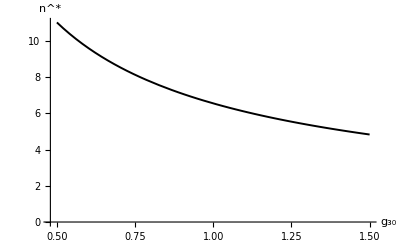

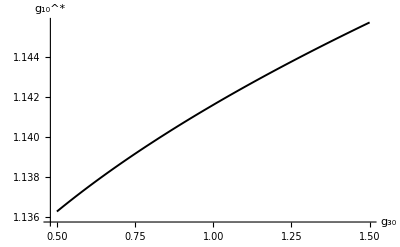

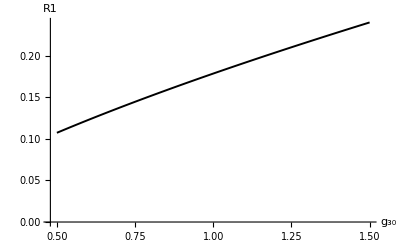

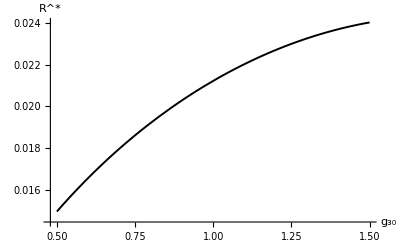

VRdatag30testXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdatag30testXY.xlsx

```mathematica
g1externalg30=1.14571+0.01;


Rdatag30testXY=Table[{0,0,0,0,0},{Length[vdatag30testXY]}];
For[i=1,i<=Length[vdatag30testXY],i++,Module[{g30,g10,n,Rstar},{g30,n,g10}=vdatag30testXY[[i,{1,2,3}]];
R1=vdatag30testXY[[i,4]];
Rstar=Sqrt[g1externalg30-g10]*R1;
Rdatag30testXY[[i]]={g30,g10,n,R1,Rstar};
Print[{g30,g10,n,R1,Rstar}];]];

VRdatag30testXY=Select[Rdatag30testXY,#[[2]]>0&];
testg30nXY=ListPlot[VRdatag30testXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testg30g10XY=ListPlot[VRdatag30testXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30R1XY=ListLinePlot[VRdatag30testXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30RXY=ListLinePlot[VRdatag30testXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatag30testXY.xlsx",VRdatag30testXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatag30testXY.xlsx",VRdatag30testXY]
```

### 2.3 Relations of KK and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;


samplePoints=E^Subdivide[Log[0.1],Log[0.5],49];
dataKKtestXY=Table[{0,0,0,0,0},{KK,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.21;
ninit=10.1;

For[i=Length[samplePoints],i>=1,i--,KK=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at KK = ",KK];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataKKtestXY[[k]]={KK,n,g10,Sqrt[R12]};
Print[{KK,n,g10,R12}];
k++;]


vdataKKtestXY=Select[dataKKtestXY,#[[2]]>0&&#[[3]]>0&];
Maxg10KKtestXY=Max[vdataKKtestXY[[All,3]]]
```

{0.5,8.2341,1.15228,0.0194}

❌ FindRoot failed at KK = 0.483844

{0.46821,8.10114,1.15134,0.0201077}

{0.453081,8.03543,1.15087,0.0204714}

❌ FindRoot failed at KK = 0.438441

{0.424274,7.90555,1.14998,0.0212188}

{0.410565,7.84137,1.14954,0.0216027}

❌ FindRoot failed at KK = 0.397299

{0.384461,7.7145,1.14868,0.0223914}

{0.372038,7.65182,1.14827,0.0227962}

{0.360017,7.58962,1.14786,0.0232083}

{0.348384,7.52792,1.14746,0.0236276}

{0.337127,7.4667,1.14706,0.0240543}

{0.326234,7.40597,1.14667,0.0244885}

{0.315693,7.34571,1.14629,0.0249302}

{0.305492,7.28593,1.14591,0.0253796}

{0.295621,7.22663,1.14554,0.0258368}

{0.286069,7.16779,1.14518,0.0263018}

{0.276825,7.10943,1.14482,0.0267748}

❌ FindRoot failed at KK = 0.26788

{0.259225,6.99408,1.14413,0.0277452}

❌ FindRoot failed at KK = 0.250848

{0.242743,6.88057,1.14346,0.0287488}

❌ FindRoot failed at KK = 0.234899

{0.227309,6.76886,1.14281,0.0297867}

{0.219965,6.71367,1.14249,0.0303187}

{0.212857,6.65893,1.14218,0.0308597}

{0.205979,6.60463,1.14187,0.0314098}

{0.199324,6.55076,1.14157,0.031969}

❌ FindRoot failed at KK = 0.192883

{0.186651,6.44431,1.14098,0.0331156}

❌ FindRoot failed at KK = 0.180619

{0.174783,6.33957,1.14041,0.0343005}

{0.169136,6.28783,1.14014,0.0349078}

{0.163671,6.23651,1.13987,0.0355251}

{0.158382,6.1856,1.1396,0.0361525}

❌ FindRoot failed at KK = 0.153264

{0.148312,6.08501,1.13908,0.0374387}

{0.14352,6.03532,1.13882,0.0380976}

❌ FindRoot failed at KK = 0.138882

{0.134395,5.93715,1.13832,0.0394482}

❌ FindRoot failed at KK = 0.130052

{0.12585,5.84056,1.13784,0.0408434}

{0.121783,5.79285,1.13761,0.0415582}

{0.117848,5.74553,1.13738,0.0422847}

❌ FindRoot failed at KK = 0.11404

{0.110356,5.65203,1.13693,0.0437735}

{0.10679,5.60584,1.13671,0.0445361}

{0.103339,5.56004,1.1365,0.0453112}

❌ FindRoot failed at KK = 0.1

1.15228

#### Graph

{0.5,1.15228,8.2341,0.139284,0.0139284}

{0.46821,1.15134,8.10114,0.141802,0.0148365}

{0.453081,1.15087,8.03543,0.143078,0.0152823}

{0.424274,1.14998,7.90555,0.145667,0.0161604}

{0.410565,1.14954,7.84137,0.146979,0.0165936}

{0.384461,1.14868,7.7145,0.149637,0.0174506}

{0.372038,1.14827,7.65182,0.150984,0.017875}

{0.360017,1.14786,7.58962,0.152343,0.0182972}

{0.348384,1.14746,7.52792,0.153713,0.0187173}

{0.337127,1.14706,7.4667,0.155095,0.0191357}

{0.326234,1.14667,7.40597,0.156488,0.0195525}

{0.315693,1.14629,7.34571,0.157893,0.019968}

{0.305492,1.14591,7.28593,0.15931,0.0203824}

{0.295621,1.14554,7.22663,0.160738,0.0207958}

{0.286069,1.14518,7.16779,0.162178,0.0212084}

{0.276825,1.14482,7.10943,0.16363,0.0216203}

{0.259225,1.14413,6.99408,0.166569,0.022443}

{0.242743,1.14346,6.88057,0.169555,0.0232646}

{0.227309,1.14281,6.76886,0.172588,0.0240863}

{0.219965,1.14249,6.71367,0.174123,0.0244974}

{0.212857,1.14218,6.65893,0.175669,0.0249088}

{0.205979,1.14187,6.60463,0.177228,0.0253205}

{0.199324,1.14157,6.55076,0.178799,0.0257328}

{0.186651,1.14098,6.44431,0.181977,0.026559}

{0.174783,1.14041,6.33957,0.185204,0.027388}

{0.169136,1.14014,6.28783,0.186836,0.0278038}

{0.163671,1.13987,6.23651,0.188481,0.0282204}

{0.158382,1.1396,6.1856,0.190138,0.0286381}

{0.148312,1.13908,6.08501,0.193491,0.0294765}

{0.14352,1.13882,6.03532,0.195186,0.0298975}

{0.134395,1.13832,5.93715,0.198616,0.030743}

{0.12585,1.13784,5.84056,0.202098,0.0315939}

{0.121783,1.13761,5.79285,0.203858,0.0320214}

{0.117848,1.13738,5.74553,0.205632,0.0324504}

{0.110356,1.13693,5.65203,0.209221,0.0333131}

{0.10679,1.13671,5.60584,0.211036,0.0337468}

{0.103339,1.1365,5.56004,0.212864,0.0341823}

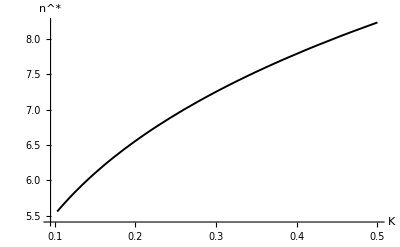

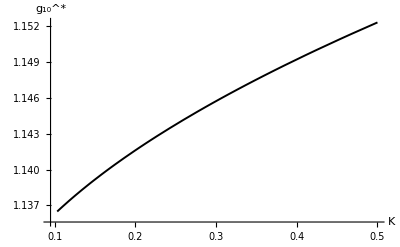

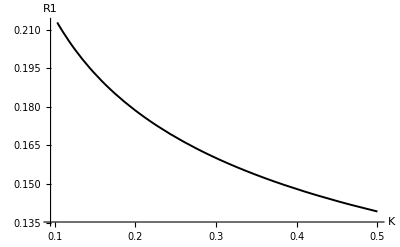

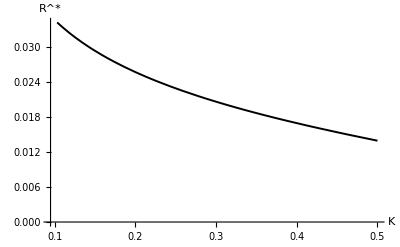

VRdataKKtestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdataKKtestXY.xlsx

```mathematica
g1externalKK=1.15228+0.01;


RdataKKtestXY=Table[{0,0,0,0,0},{Length[vdataKKtestXY]}];
For[i=1,i<=Length[vdataKKtestXY],i++,Module[{KK,g10,n,Rstar},{KK,n,g10}=vdataKKtestXY[[i,{1,2,3}]];
R1=vdataKKtestXY[[i,4]];
Rstar=Sqrt[g1externalKK-g10]*R1;
RdataKKtestXY[[i]]={KK,g10,n,R1,Rstar};
Print[{KK,g10,n,R1,Rstar}];]];

VRdataKKtestXY=Select[RdataKKtestXY,#[[2]]>0&];
testKKnXY=ListPlot[VRdataKKtestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testKKg10XY=ListPlot[VRdataKKtestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKR1XY=ListLinePlot[VRdataKKtestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKRXY=ListLinePlot[VRdataKKtestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataKKtestXY.xlsx",VRdataKKtestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdataKKtestXY.xlsx",VRdataKKtestXY]
```

## 3. parametric study for skin fiber

### 3.1 Relations of beta and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;h=1.0/75;g12=1;
cf=100;phif=0.05;lamdaf=0.885;


betamin=0;
betamax=Pi/2;
samplePoints=Subdivide[ betamin, betamax,49];
databetatestXY=Table[{0,0,0,0,0,0},{ beta,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;

g10init=1.193;
ninit=6.492;

For[i=Length[samplePoints],i>=1,i--, beta=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  beta = ", beta];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
databetatestXY[[k]]={ beta,n,g10,Sqrt[R12]};
Print[{ beta,n,g10,Sqrt[R12]}];
k++;]


vdatabetatestXY=Select[databetatestXY,#[[2]]>0&&#[[3]]>0&];
Maxg10betatestXY=Max[vdatabetatestXY[[All,3]]]
```

{π/2,8.49417,1.02191,0.15655}

{(24 π)/49,8.48798,1.0225,0.156614}

{(47 π)/98,8.46944,1.02427,0.156806}

{(23 π)/49,8.43863,1.02718,0.157122}

{(45 π)/98,8.39576,1.03118,0.157555}

{(22 π)/49,8.34123,1.03621,0.158098}

{(43 π)/98,8.27568,1.04215,0.158738}

{(3 π)/7,8.20009,1.04889,0.159466}

{(41 π)/98,8.11569,1.05628,0.160267}

{(20 π)/49,8.02398,1.06415,0.161129}

{(39 π)/98,7.92663,1.07232,0.162041}

{(19 π)/49,7.82533,1.0806,0.162992}

{(37 π)/98,7.72173,1.08882,0.163971}

{(18 π)/49,7.61728,1.09679,0.164973}

{(5 π)/14,7.51324,1.10437,0.165993}

{(17 π)/49,7.41057,1.11142,0.167029}

{(33 π)/98,7.30997,1.11783,0.168081}

{(16 π)/49,7.21188,1.12352,0.169153}

{(31 π)/98,7.1165,1.12843,0.17025}

{(15 π)/49,7.02387,1.13254,0.171381}

{(29 π)/98,6.93389,1.13584,0.172556}

{(2 π)/7,6.84636,1.13835,0.173783}

{(27 π)/98,6.76107,1.14011,0.175075}

{(13 π)/49,6.6778,1.14117,0.176438}

{(25 π)/98,6.59636,1.1416,0.177882}

{(12 π)/49,6.51664,1.14147,0.179412}

{(23 π)/98,6.43857,1.14086,0.181029}

{(11 π)/49,6.36219,1.13985,0.182734}

{(3 π)/14,6.28759,1.13852,0.184524}

{(10 π)/49,6.2149,1.13694,0.186392}

{(19 π)/98,6.14434,1.13517,0.18833}

{(9 π)/49,6.0761,1.13328,0.190328}

{(17 π)/98,6.01044,1.13132,0.192374}

{(8 π)/49,5.94757,1.12933,0.194454}

{(15 π)/98,5.88772,1.12735,0.196554}

{π/7,5.83109,1.12542,0.198656}

{(13 π)/98,5.77785,1.12356,0.200743}

{(6 π)/49,5.72815,1.12179,0.202796}

{(11 π)/98,5.68214,1.12013,0.204797}

{(5 π)/49,5.63991,1.11859,0.206724}

{(9 π)/98,5.60154,1.11717,0.208556}

{(4 π)/49,5.5671,1.1159,0.210271}

{π/14,5.53663,1.11476,0.211848}

{(3 π)/49,5.51019,1.11378,0.213266}

{(5 π)/98,5.48778,1.11294,0.214506}

{(2 π)/49,5.46943,1.11225,0.215547}

{(3 π)/98,5.45515,1.11171,0.216375}

{π/49,5.44494,1.11133,0.216977}

{π/98,5.43882,1.1111,0.217342}

{0,5.43678,1.11102,0.217464}

1.1416

#### Graph

{π/2,1.02191,8.49417,0.15655,0.0563772}

{(24 π)/49,1.0225,8.48798,0.156614,0.0562716}

{(47 π)/98,1.02427,8.46944,0.156806,0.0559539}

{(23 π)/49,1.02718,8.43863,0.157122,0.055422}

{(45 π)/98,1.03118,8.39576,0.157555,0.0546732}

{(22 π)/49,1.03621,8.34123,0.158098,0.0537047}

{(43 π)/98,1.04215,8.27568,0.158738,0.052515}

{(3 π)/7,1.04889,8.20009,0.159466,0.0511054}

{(41 π)/98,1.05628,8.11569,0.160267,0.0494805}

{(20 π)/49,1.06415,8.02398,0.161129,0.0476495}

{(39 π)/98,1.07232,7.92663,0.162041,0.0456264}

{(19 π)/49,1.0806,7.82533,0.162992,0.0434304}

{(37 π)/98,1.08882,7.72173,0.163971,0.041086}

{(18 π)/49,1.09679,7.61728,0.164973,0.0386225}

{(5 π)/14,1.10437,7.51324,0.165993,0.0360742}

{(17 π)/49,1.11142,7.41057,0.167029,0.0334807}

{(33 π)/98,1.11783,7.30997,0.168081,0.030887}

{(16 π)/49,1.12352,7.21188,0.169153,0.0283447}

{(31 π)/98,1.12843,7.1165,0.17025,0.0259128}

{(15 π)/49,1.13254,7.02387,0.171381,0.0236592}

{(29 π)/98,1.13584,6.93389,0.172556,0.0216612}

{(2 π)/7,1.13835,6.84636,0.173783,0.0200026}

{(27 π)/98,1.14011,6.76107,0.175075,0.0187663}

{(13 π)/49,1.14117,6.6778,0.176438,0.0180183}

{(25 π)/98,1.1416,6.59636,0.177882,0.0177882}

{(12 π)/49,1.14147,6.51664,0.179412,0.0180565}

{(23 π)/98,1.14086,6.43857,0.181029,0.0187588}

{(11 π)/49,1.13985,6.36219,0.182734,0.0198056}

{(3 π)/14,1.13852,6.28759,0.184524,0.0211038}

{(10 π)/49,1.13694,6.2149,0.186392,0.0225712}

{(19 π)/98,1.13517,6.14434,0.18833,0.0241413}

{(9 π)/49,1.13328,6.0761,0.190328,0.0257633}

{(17 π)/98,1.13132,6.01044,0.192374,0.0273991}

{(8 π)/49,1.12933,5.94757,0.194454,0.0290207}

{(15 π)/98,1.12735,5.88772,0.196554,0.0306071}

{π/7,1.12542,5.83109,0.198656,0.0321425}

{(13 π)/98,1.12356,5.77785,0.200743,0.0336147}

{(6 π)/49,1.12179,5.72815,0.202796,0.0350138}

{(11 π)/98,1.12013,5.68214,0.204797,0.0363319}

{(5 π)/49,1.11859,5.63991,0.206724,0.0375617}

{(9 π)/98,1.11717,5.60154,0.208556,0.0386969}

{(4 π)/49,1.1159,5.5671,0.210271,0.0397315}

{π/14,1.11476,5.53663,0.211848,0.0406601}

{(3 π)/49,1.11378,5.51019,0.213266,0.0414772}

{(5 π)/98,1.11294,5.48778,0.214506,0.0421781}

{(2 π)/49,1.11225,5.46943,0.215547,0.0427583}

{(3 π)/98,1.11171,5.45515,0.216375,0.0432139}

{π/49,1.11133,5.44494,0.216977,0.0435417}

{π/98,1.1111,5.43882,0.217342,0.0437393}

{0,1.11102,5.43678,0.217464,0.0438054}

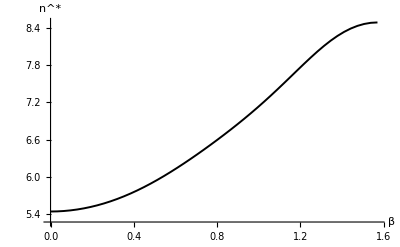

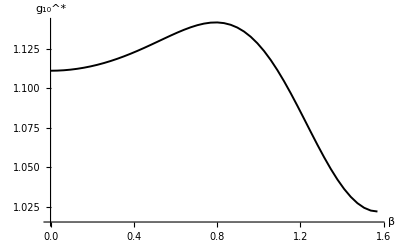

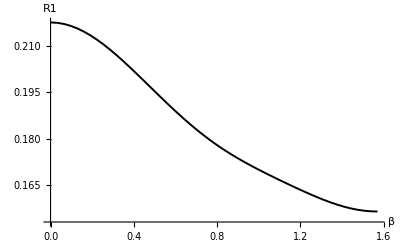

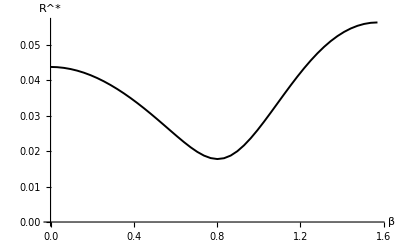

VRdatabetatestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdatabetatestXY.xlsx

```mathematica
g1externalbeta=1.1416+0.01;


RdatabetatestXY=Table[{0,0,0,0,0},{Length[vdatabetatestXY]}];
For[i=1,i<=Length[vdatabetatestXY],i++,Module[{beta,g10,n,Rstar},{beta,n,g10}=vdatabetatestXY[[i,{1,2,3}]];
R1=vdatabetatestXY[[i,4]];
Rstar=Sqrt[g1externalbeta-g10]*R1;
RdatabetatestXY[[i]]={beta,g10,n,R1,Rstar};
Print[{beta,g10,n,R1,Rstar}];]];

VRdatabetatestXY=Select[RdatabetatestXY,#[[2]]>0&];
testbetanXY=ListPlot[VRdatabetatestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testbetag10XY=ListPlot[VRdatabetatestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaR1XY=ListLinePlot[VRdatabetatestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaRXY=ListLinePlot[VRdatabetatestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatabetatestXY.xlsx",VRdatabetatestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatabetatestXY.xlsx",VRdatabetatestXY]
```

### 3.2 Relations of lamdaf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;KK=0.2;g12=1;
cf=100;phif=0.05;beta=Pi/4;


samplePoints=Subdivide[0.1,1,50];

datalamdaftestXY=Table[{0,0,0,0,0},{ lamdaf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, lamdaf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  lamdaf = ", lamdaf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datalamdaftestXY[[k]]={ lamdaf,n,g10,Sqrt[R12]};
Print[{ lamdaf,n,g10,R12}];
k++;]


vdatalamdaftestXY=Select[datalamdaftestXY,#[[2]]>0&&#[[3]]>0&];
MaxlamdaftestXY=Max[vdatalamdaftestXY[[All,3]]]
```

{1.,6.99663,1.01435,0.0304219}

{0.982,6.93404,1.03533,0.0304711}

{0.964,6.86786,1.05601,0.030611}

{0.946,6.79895,1.07632,0.0308237}

{0.928,6.7282,1.09619,0.0310948}

{0.91,6.65641,1.11557,0.0314122}

{0.892,6.58429,1.13442,0.0317656}

{0.874,6.51248,1.15271,0.0321465}

{0.856,6.44151,1.17042,0.0325474}

{0.838,6.37181,1.18753,0.0329624}

{0.82,6.30372,1.20404,0.0333863}

{0.802,6.2375,1.21996,0.0338149}

❌ FindRoot failed at  lamdaf = 0.784

❌ FindRoot failed at  lamdaf = 0.766

{0.748,6.0517,1.2642,0.0350967}

{0.73,5.99434,1.27781,0.0355149}

{0.712,5.9393,1.29088,0.0359258}

{0.694,5.88657,1.30342,0.0363282}

{0.676,5.83612,1.31545,0.0367213}

{0.658,5.78792,1.32698,0.0371042}

{0.64,5.74189,1.33803,0.0374765}

{0.622,5.69798,1.34862,0.0378379}

{0.604,5.65612,1.35876,0.038188}

{0.586,5.61625,1.36846,0.0385267}

{0.568,5.57829,1.37775,0.0388539}

{0.55,5.54218,1.38663,0.0391695}

{0.532,5.50785,1.39511,0.0394736}

{0.514,5.47523,1.40321,0.0397661}

{0.496,5.44425,1.41094,0.0400472}

{0.478,5.41487,1.41832,0.0403169}

{0.46,5.38701,1.42534,0.0405753}

{0.442,5.36063,1.43203,0.0408226}

{0.424,5.33567,1.43838,0.0410588}

{0.406,5.31208,1.44441,0.0412841}

{0.388,5.28981,1.45013,0.0414986}

{0.37,5.26883,1.45555,0.0417024}

{0.352,5.24908,1.46066,0.0418956}

{0.334,5.23054,1.46549,0.0420785}

{0.316,5.21317,1.47002,0.042251}

{0.298,5.19692,1.47428,0.0424133}

{0.28,5.18178,1.47826,0.0425655}

{0.262,5.16771,1.48197,0.0427078}

{0.244,5.15469,1.48542,0.0428401}

{0.226,5.14269,1.4886,0.0429626}

{0.208,5.13169,1.49153,0.0430755}

❌ FindRoot failed at  lamdaf = 0.19

{0.172,5.11262,1.49662,0.0432723}

{0.154,5.10451,1.49879,0.0433564}

{0.136,5.09734,1.50071,0.0434311}

{0.118,5.09108,1.5024,0.0434964}

{0.1,5.08573,1.50384,0.0435523}

1.50384

#### Graph

{1.,1.01435,6.99663,0.174419,0.12327}

{0.982,1.03533,6.93404,0.17456,0.12075}

{0.964,1.05601,6.86786,0.17496,0.118383}

{0.946,1.07632,6.79895,0.175567,0.116129}

{0.928,1.09619,6.7282,0.176337,0.113959}

{0.91,1.11557,6.65641,0.177235,0.11185}

{0.892,1.13442,6.58429,0.178229,0.109783}

{0.874,1.15271,6.51248,0.179294,0.107745}

{0.856,1.17042,6.44151,0.180409,0.105724}

{0.838,1.18753,6.37181,0.181556,0.103711}

{0.82,1.20404,6.30372,0.182719,0.1017}

{0.802,1.21996,6.2375,0.183888,0.0996865}

{0.748,1.2642,6.0517,0.187341,0.0936031}

{0.73,1.27781,5.99434,0.188454,0.0915561}

{0.712,1.29088,5.9393,0.189541,0.0894986}

{0.694,1.30342,5.88657,0.1906,0.0874309}

{0.676,1.31545,5.83612,0.191628,0.0853531}

{0.658,1.32698,5.78792,0.192625,0.0832659}

{0.64,1.33803,5.74189,0.193589,0.08117}

{0.622,1.34862,5.69798,0.19452,0.0790661}

{0.604,1.35876,5.65612,0.195418,0.0769552}

{0.586,1.36846,5.61625,0.196282,0.074838}

{0.568,1.37775,5.57829,0.197114,0.0727155}

{0.55,1.38663,5.54218,0.197913,0.0705886}

{0.532,1.39511,5.50785,0.19868,0.0684583}

{0.514,1.40321,5.47523,0.199414,0.0663256}

{0.496,1.41094,5.44425,0.200118,0.0641913}

{0.478,1.41832,5.41487,0.200791,0.0620567}

{0.46,1.42534,5.38701,0.201433,0.0599226}

{0.442,1.43203,5.36063,0.202046,0.0577902}

{0.424,1.43838,5.33567,0.20263,0.0556607}

{0.406,1.44441,5.31208,0.203185,0.0535353}

{0.388,1.45013,5.28981,0.203712,0.0514154}

{0.37,1.45555,5.26883,0.204212,0.0493026}

{0.352,1.46066,5.24908,0.204684,0.0471986}

{0.334,1.46549,5.23054,0.20513,0.0451052}

{0.316,1.47002,5.21317,0.20555,0.0430248}

{0.298,1.47428,5.19692,0.205945,0.0409599}

{0.28,1.47826,5.18178,0.206314,0.0389136}

{0.262,1.48197,5.16771,0.206659,0.0368895}

{0.244,1.48542,5.15469,0.206979,0.0348921}

{0.226,1.4886,5.14269,0.207274,0.0329267}

{0.208,1.49153,5.13169,0.207546,0.0309998}

{0.172,1.49662,5.11262,0.20802,0.027296}

{0.154,1.49879,5.10451,0.208222,0.0255417}

{0.136,1.50071,5.09734,0.208401,0.0238721}

{0.118,1.5024,5.09108,0.208558,0.0223067}

{0.1,1.50384,5.08573,0.208692,0.0208692}

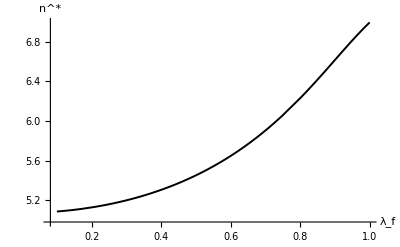

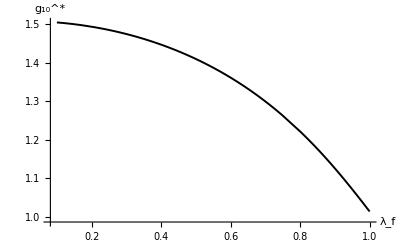

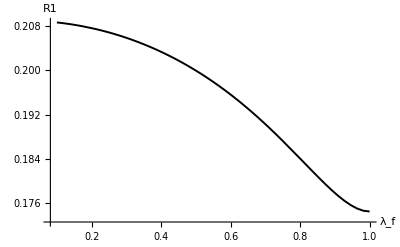

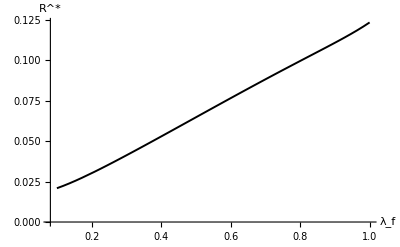

VRdatalamdaftestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdatalamdaftestXY.xlsx

```mathematica
g1externallamdaf=1.50384+0.01;


RdatalamdaftestXY=Table[{0,0,0,0,0},{Length[vdatalamdaftestXY]}];
For[i=1,i<=Length[vdatalamdaftestXY],i++,Module[{lamdaf,g10,n,Rstar},{lamdaf,n,g10}=vdatalamdaftestXY[[i,{1,2,3}]];
R1=vdatalamdaftestXY[[i,4]];
Rstar=Sqrt[g1externallamdaf-g10]*R1;
RdatalamdaftestXY[[i]]={lamdaf,g10,n,R1,Rstar};
Print[{lamdaf,g10,n,R1,Rstar}];]];

VRdatalamdaftestXY=Select[RdatalamdaftestXY,#[[2]]>0&];
testlamdafnXY=ListPlot[VRdatalamdaftestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testlamdafg10XY=ListPlot[VRdatalamdaftestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafR1XY=ListLinePlot[VRdatalamdaftestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafRXY=ListLinePlot[VRdatalamdaftestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatalamdaftestXY.xlsx",VRdatalamdaftestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatalamdaftestXY.xlsx",VRdatalamdaftestXY]
```

### 3.3 Relations of cf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
phif=0.05;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[50,100,100];
datacftestXY=Table[{0,0,0,0,0},{ cf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, cf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  cf = ", cf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datacftestXY[[k]]={ cf,n,g10,Sqrt[R12]};
Print[{ cf,n,g10,R12}];
k++;]


vdatacftestXY=Select[datacftestXY,#[[2]]>0&&#[[3]]>0&];
MaxcftestXY=Max[vdatacftestXY[[All,3]]]
```

{100,6.55629,1.1416,0.0319109}

{199/2,6.56063,1.14129,0.0318831}

{99,6.565,1.14098,0.0318553}

{197/2,6.56938,1.14067,0.0318274}

{98,6.57378,1.14036,0.0317994}

{195/2,6.5782,1.14005,0.0317714}

{97,6.58264,1.13974,0.0317434}

{193/2,6.5871,1.13942,0.0317152}

{96,6.59158,1.1391,0.031687}

{191/2,6.59608,1.13878,0.0316588}

{95,6.60061,1.13847,0.0316304}

{189/2,6.60515,1.13814,0.031602}

{94,6.60972,1.13782,0.0315736}

{187/2,6.6143,1.1375,0.0315451}

{93,6.61891,1.13717,0.0315165}

{185/2,6.62354,1.13685,0.0314878}

{92,6.6282,1.13652,0.0314591}

{183/2,6.63287,1.13619,0.0314304}

{91,6.63757,1.13586,0.0314015}

{181/2,6.64229,1.13553,0.0313726}

{90,6.64703,1.13519,0.0313436}

{179/2,6.6518,1.13486,0.0313146}

{89,6.65659,1.13452,0.0312855}

{177/2,6.6614,1.13418,0.0312563}

{88,6.66624,1.13384,0.0312271}

{175/2,6.6711,1.1335,0.0311977}

{87,6.67599,1.13316,0.0311683}

{173/2,6.6809,1.13281,0.0311389}

{86,6.68583,1.13247,0.0311094}

{171/2,6.69079,1.13212,0.0310798}

{85,6.69578,1.13177,0.0310501}

{169/2,6.70079,1.13142,0.0310203}

{84,6.70582,1.13107,0.0309905}

{167/2,6.71089,1.13071,0.0309606}

{83,6.71598,1.13036,0.0309307}

{165/2,6.72109,1.13,0.0309006}

{82,6.72623,1.12964,0.0308705}

{163/2,6.7314,1.12928,0.0308403}

{81,6.7366,1.12892,0.0308101}

{161/2,6.74182,1.12855,0.0307797}

{80,6.74707,1.12819,0.0307493}

{159/2,6.75235,1.12782,0.0307188}

{79,6.75766,1.12745,0.0306883}

{157/2,6.76299,1.12708,0.0306576}

{78,6.76836,1.1267,0.0306269}

{155/2,6.77376,1.12633,0.0305961}

{77,6.77918,1.12595,0.0305652}

{153/2,6.78463,1.12557,0.0305342}

{76,6.79012,1.12519,0.0305032}

{151/2,6.79563,1.12481,0.0304721}

{75,6.80118,1.12443,0.0304409}

{149/2,6.80676,1.12404,0.0304096}

{74,6.81237,1.12365,0.0303782}

{147/2,6.81801,1.12326,0.0303467}

{73,6.82368,1.12287,0.0303152}

{145/2,6.82939,1.12248,0.0302835}

{72,6.83512,1.12208,0.0302518}

{143/2,6.8409,1.12168,0.03022}

{71,6.8467,1.12128,0.0301881}

{141/2,6.85254,1.12088,0.0301562}

{70,6.85842,1.12047,0.0301241}

{139/2,6.86432,1.12007,0.0300919}

{69,6.87027,1.11966,0.0300597}

{137/2,6.87625,1.11925,0.0300274}

{68,6.88226,1.11883,0.0299949}

{135/2,6.88832,1.11842,0.0299624}

{67,6.89441,1.118,0.0299298}

{133/2,6.90053,1.11758,0.0298971}

{66,6.9067,1.11716,0.0298643}

{131/2,6.9129,1.11673,0.0298314}

{65,6.91914,1.11631,0.0297984}

{129/2,6.92542,1.11588,0.0297653}

{64,6.93174,1.11545,0.0297322}

{127/2,6.9381,1.11501,0.0296989}

{63,6.9445,1.11458,0.0296655}

{125/2,6.95094,1.11414,0.0296321}

{62,6.95743,1.1137,0.0295985}

{123/2,6.96395,1.11325,0.0295648}

{61,6.97052,1.11281,0.029531}

{121/2,6.97713,1.11236,0.0294972}

{60,6.98379,1.11191,0.0294632}

{119/2,6.99049,1.11145,0.0294291}

{59,6.99723,1.111,0.0293949}

{117/2,7.00402,1.11054,0.0293606}

{58,7.01085,1.11008,0.0293263}

{115/2,7.01773,1.10961,0.0292918}

{57,7.02466,1.10915,0.0292572}

{113/2,7.03164,1.10868,0.0292224}

{56,7.03866,1.1082,0.0291876}

{111/2,7.04574,1.10773,0.0291527}

{55,7.05286,1.10725,0.0291176}

{109/2,7.06004,1.10677,0.0290825}

{54,7.06726,1.10628,0.0290472}

{107/2,7.07454,1.1058,0.0290119}

{53,7.08187,1.10531,0.0289764}

{105/2,7.08925,1.10481,0.0289408}

{52,7.09669,1.10432,0.028905}

{103/2,7.10418,1.10382,0.0288692}

{51,7.11172,1.10331,0.0288332}

{101/2,7.11933,1.10281,0.0287972}

{50,7.12699,1.1023,0.028761}

1.1416

#### Graph

{100,1.1416,6.55629,0.178636,0.0178636}

{199/2,1.14129,6.56063,0.178558,0.0181284}

{99,1.14098,6.565,0.17848,0.0183901}

{197/2,1.14067,6.56938,0.178402,0.0186486}

{98,1.14036,6.57378,0.178324,0.0189043}

{195/2,1.14005,6.5782,0.178245,0.0191572}

{97,1.13974,6.58264,0.178167,0.0194074}

{193/2,1.13942,6.5871,0.178088,0.019655}

{96,1.1391,6.59158,0.178008,0.0199001}

{191/2,1.13878,6.59608,0.177929,0.0201429}

{95,1.13847,6.60061,0.177849,0.0203833}

{189/2,1.13814,6.60515,0.17777,0.0206216}

{94,1.13782,6.60972,0.17769,0.0208577}

{187/2,1.1375,6.6143,0.177609,0.0210918}

{93,1.13717,6.61891,0.177529,0.0213238}

{185/2,1.13685,6.62354,0.177448,0.021554}

{92,1.13652,6.6282,0.177367,0.0217823}

{183/2,1.13619,6.63287,0.177286,0.0220088}

{91,1.13586,6.63757,0.177205,0.0222336}

{181/2,1.13553,6.64229,0.177123,0.0224567}

{90,1.13519,6.64703,0.177041,0.0226782}

{179/2,1.13486,6.6518,0.176959,0.0228981}

{89,1.13452,6.65659,0.176877,0.0231165}

{177/2,1.13418,6.6614,0.176795,0.0233335}

{88,1.13384,6.66624,0.176712,0.0235489}

{175/2,1.1335,6.6711,0.176629,0.023763}

{87,1.13316,6.67599,0.176546,0.0239758}

{173/2,1.13281,6.6809,0.176462,0.0241872}

{86,1.13247,6.68583,0.176378,0.0243974}

{171/2,1.13212,6.69079,0.176295,0.0246063}

{85,1.13177,6.69578,0.17621,0.0248141}

{169/2,1.13142,6.70079,0.176126,0.0250206}

{84,1.13107,6.70582,0.176041,0.0252261}

{167/2,1.13071,6.71089,0.175956,0.0254304}

{83,1.13036,6.71598,0.175871,0.0256337}

{165/2,1.13,6.72109,0.175786,0.0258359}

{82,1.12964,6.72623,0.1757,0.0260371}

{163/2,1.12928,6.7314,0.175614,0.0262373}

{81,1.12892,6.7366,0.175528,0.0264366}

{161/2,1.12855,6.74182,0.175442,0.0266349}

{80,1.12819,6.74707,0.175355,0.0268323}

{159/2,1.12782,6.75235,0.175268,0.0270288}

{79,1.12745,6.75766,0.175181,0.0272245}

{157/2,1.12708,6.76299,0.175093,0.0274193}

{78,1.1267,6.76836,0.175005,0.0276133}

{155/2,1.12633,6.77376,0.174917,0.0278065}

{77,1.12595,6.77918,0.174829,0.0279989}

{153/2,1.12557,6.78463,0.17474,0.0281906}

{76,1.12519,6.79012,0.174652,0.0283815}

{151/2,1.12481,6.79563,0.174562,0.0285717}

{75,1.12443,6.80118,0.174473,0.0287612}

{149/2,1.12404,6.80676,0.174383,0.0289501}

{74,1.12365,6.81237,0.174293,0.0291382}

{147/2,1.12326,6.81801,0.174203,0.0293258}

{73,1.12287,6.82368,0.174113,0.0295126}

{145/2,1.12248,6.82939,0.174022,0.0296989}

{72,1.12208,6.83512,0.173931,0.0298846}

{143/2,1.12168,6.8409,0.173839,0.0300697}

{71,1.12128,6.8467,0.173747,0.0302542}

{141/2,1.12088,6.85254,0.173655,0.0304382}

{70,1.12047,6.85842,0.173563,0.0306216}

{139/2,1.12007,6.86432,0.17347,0.0308045}

{69,1.11966,6.87027,0.173377,0.0309869}

{137/2,1.11925,6.87625,0.173284,0.0311688}

{68,1.11883,6.88226,0.17319,0.0313503}

{135/2,1.11842,6.88832,0.173097,0.0315312}

{67,1.118,6.89441,0.173002,0.0317117}

{133/2,1.11758,6.90053,0.172908,0.0318918}

{66,1.11716,6.9067,0.172813,0.0320714}

{131/2,1.11673,6.9129,0.172718,0.0322506}

{65,1.11631,6.91914,0.172622,0.0324294}

{129/2,1.11588,6.92542,0.172526,0.0326078}

{64,1.11545,6.93174,0.17243,0.0327858}

{127/2,1.11501,6.9381,0.172334,0.0329634}

{63,1.11458,6.9445,0.172237,0.0331407}

{125/2,1.11414,6.95094,0.17214,0.0333176}

{62,1.1137,6.95743,0.172042,0.0334942}

{123/2,1.11325,6.96395,0.171944,0.0336704}

{61,1.11281,6.97052,0.171846,0.0338464}

{121/2,1.11236,6.97713,0.171747,0.034022}

{60,1.11191,6.98379,0.171648,0.0341973}

{119/2,1.11145,6.99049,0.171549,0.0343724}

{59,1.111,6.99723,0.17145,0.0345471}

{117/2,1.11054,7.00402,0.171349,0.0347216}

{58,1.11008,7.01085,0.171249,0.0348958}

{115/2,1.10961,7.01773,0.171148,0.0350698}

{57,1.10915,7.02466,0.171047,0.0352436}

{113/2,1.10868,7.03164,0.170946,0.0354171}

{56,1.1082,7.03866,0.170844,0.0355904}

{111/2,1.10773,7.04574,0.170742,0.0357635}

{55,1.10725,7.05286,0.170639,0.0359363}

{109/2,1.10677,7.06004,0.170536,0.036109}

{54,1.10628,7.06726,0.170432,0.0362815}

{107/2,1.1058,7.07454,0.170329,0.0364539}

{53,1.10531,7.08187,0.170224,0.036626}

{105/2,1.10481,7.08925,0.17012,0.036798}

{52,1.10432,7.09669,0.170015,0.0369699}

{103/2,1.10382,7.10418,0.169909,0.0371416}

{51,1.10331,7.11172,0.169804,0.0373132}

{101/2,1.10281,7.11933,0.169697,0.0374847}

{50,1.1023,7.12699,0.169591,0.0376561}

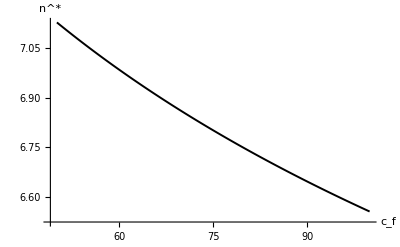

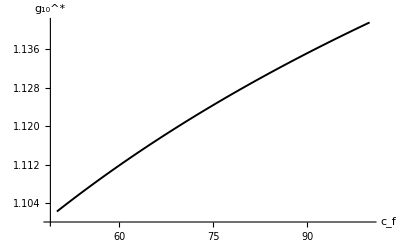

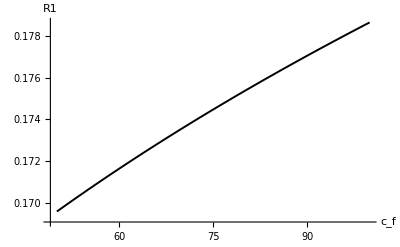

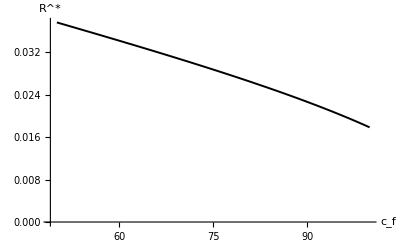

VRdatacftestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdatacftestXY.xlsx

```mathematica
g1externalcf=1.1416+0.01;


RdatacftestXY=Table[{0,0,0,0,0},{Length[vdatacftestXY]}];
For[i=1,i<=Length[vdatacftestXY],i++,Module[{cf,g10,n,Rstar},{cf,n,g10}=vdatacftestXY[[i,{1,2,3}]];
R1=vdatacftestXY[[i,4]];
Rstar=Sqrt[g1externalcf-g10]*R1;
RdatacftestXY[[i]]={cf,g10,n,R1,Rstar};
Print[{cf,g10,n,R1,Rstar}];]];

VRdatacftestXY=Select[RdatacftestXY,#[[2]]>0&];
testcfnXY=ListPlot[VRdatacftestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testcfg10XY=ListPlot[VRdatacftestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfR1XY=ListLinePlot[VRdatacftestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfRXY=ListLinePlot[VRdatacftestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatacftestXY.xlsx",VRdatacftestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatacftestXY.xlsx",VRdatacftestXY]
```

### 3.4 Relations of phif and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
cf=100;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[0,0.1,50];
dataphiftestXY=Table[{0,0,0,0,0},{ phif,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, phif=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  phif = ", phif];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataphiftestXY[[k]]={ phif,n,g10,Sqrt[R12]};
Print[{ phif,n,g10,R12}];
k++;]


vdataphiftestXY=Select[dataphiftestXY,#[[2]]>0&&#[[3]]>0&];
MaxphiftestXY=Max[vdataphiftestXY[[All,3]]]
```

{0.1,5.97193,1.18971,0.0359815}

❌ FindRoot failed at  phif = 0.098

{0.096,6.00666,1.18675,0.0357022}

{0.094,6.02457,1.18523,0.0355603}

{0.092,6.04286,1.18368,0.0354169}

{0.09,6.06155,1.1821,0.0352718}

{0.088,6.08066,1.18048,0.0351252}

{0.086,6.1002,1.17884,0.0349767}

{0.084,6.1202,1.17716,0.0348265}

{0.082,6.14067,1.17544,0.0346744}

{0.08,6.16163,1.17369,0.0345204}

{0.078,6.18311,1.17189,0.0343643}

{0.076,6.20514,1.17006,0.0342061}

{0.074,6.22773,1.16819,0.0340457}

{0.072,6.25093,1.16627,0.0338831}

{0.07,6.27475,1.1643,0.0337181}

{0.068,6.29923,1.16229,0.0335505}

{0.066,6.32441,1.16023,0.0333804}

{0.064,6.35032,1.15811,0.0332076}

{0.062,6.37701,1.15594,0.0330319}

{0.06,6.40453,1.15372,0.0328533}

{0.058,6.43291,1.15143,0.0326716}

{0.056,6.46222,1.14908,0.0324867}

{0.054,6.49251,1.14666,0.0322984}

{0.052,6.52384,1.14417,0.0321065}

{0.05,6.55629,1.1416,0.0319109}

{0.048,6.58994,1.13896,0.0317114}

{0.046,6.62486,1.13623,0.0315077}

{0.044,6.66116,1.13341,0.0312997}

{0.042,6.69893,1.13049,0.0310871}

{0.04,6.7383,1.12748,0.0308697}

{0.038,6.7794,1.12435,0.0306472}

{0.036,6.82237,1.12111,0.0304193}

{0.034,6.86738,1.11774,0.0301857}

{0.032,6.91463,1.11423,0.0299461}

{0.03,6.96432,1.11058,0.0297}

{0.028,7.01672,1.10677,0.0294472}

{0.026,7.0721,1.10279,0.0291871}

{0.024,7.13081,1.09862,0.0289193}

{0.022,7.19325,1.09423,0.0286435}

{0.02,7.25987,1.08962,0.0283589}

{0.018,7.33125,1.08475,0.0280652}

{0.016,7.40806,1.0796,0.0277619}

{0.014,7.49113,1.07413,0.0274485}

{0.012,7.58151,1.06829,0.0271246}

{0.01,7.68049,1.06203,0.0267902}

{0.008,7.78977,1.05529,0.0264456}

{0.006,7.91157,1.04798,0.026092}

{0.004,8.0489,1.03999,0.0257323}

{0.002,8.20596,1.03118,0.0253727}

{0.,8.38891,1.02135,0.0250261}

1.18971

#### Graph

{0.1,1.18971,5.97193,0.189688,0.0189688}

{0.096,1.18675,6.00666,0.18895,0.0215082}

{0.094,1.18523,6.02457,0.188574,0.0226904}

{0.092,1.18368,6.04286,0.188194,0.0238266}

{0.09,1.1821,6.06155,0.187808,0.0249232}

{0.088,1.18048,6.08066,0.187417,0.0259857}

{0.086,1.17884,6.1002,0.187021,0.0270185}

{0.084,1.17716,6.1202,0.186619,0.0280251}

{0.082,1.17544,6.14067,0.186211,0.0290087}

{0.08,1.17369,6.16163,0.185797,0.0299719}

{0.078,1.17189,6.18311,0.185376,0.0309168}

{0.076,1.17006,6.20514,0.184949,0.0318457}

{0.074,1.16819,6.22773,0.184515,0.0327601}

{0.072,1.16627,6.25093,0.184074,0.0336616}

{0.07,1.1643,6.27475,0.183625,0.0345517}

{0.068,1.16229,6.29923,0.183168,0.0354317}

{0.066,1.16023,6.32441,0.182703,0.0363026}

{0.064,1.15811,6.35032,0.18223,0.0371655}

{0.062,1.15594,6.37701,0.181747,0.0380216}

{0.06,1.15372,6.40453,0.181255,0.0388716}

{0.058,1.15143,6.43291,0.180753,0.0397165}

{0.056,1.14908,6.46222,0.180241,0.0405571}

{0.054,1.14666,6.49251,0.179718,0.0413943}

{0.052,1.14417,6.52384,0.179183,0.0422287}

{0.05,1.1416,6.55629,0.178636,0.0430612}

{0.048,1.13896,6.58994,0.178077,0.0438925}

{0.046,1.13623,6.62486,0.177504,0.0447234}

{0.044,1.13341,6.66116,0.176917,0.0455546}

{0.042,1.13049,6.69893,0.176315,0.0463868}

{0.04,1.12748,6.7383,0.175698,0.047221}

{0.038,1.12435,6.7794,0.175063,0.0480578}

{0.036,1.12111,6.82237,0.174411,0.0488981}

{0.034,1.11774,6.86738,0.17374,0.0497428}

{0.032,1.11423,6.91463,0.173049,0.0505929}

{0.03,1.11058,6.96432,0.172337,0.0514494}

{0.028,1.10677,7.01672,0.171602,0.0523135}

{0.026,1.10279,7.0721,0.170842,0.0531865}

{0.024,1.09862,7.13081,0.170057,0.0540698}

{0.022,1.09423,7.19325,0.169244,0.054965}

{0.02,1.08962,7.25987,0.168401,0.0558742}

{0.018,1.08475,7.33125,0.167527,0.0567996}

{0.016,1.0796,7.40806,0.166619,0.0577441}

{0.014,1.07413,7.49113,0.165676,0.0587112}

{0.012,1.06829,7.58151,0.164696,0.0597052}

{0.01,1.06203,7.68049,0.163677,0.0607322}

{0.008,1.05529,7.78977,0.162621,0.0617999}

{0.006,1.04798,7.91157,0.16153,0.0629196}

{0.004,1.03999,8.0489,0.160413,0.0641078}

{0.002,1.03118,8.20596,0.159288,0.0653903}

{0.,1.02135,8.38891,0.158196,0.0668105}

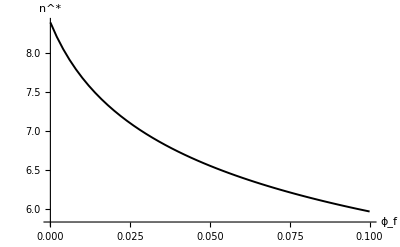

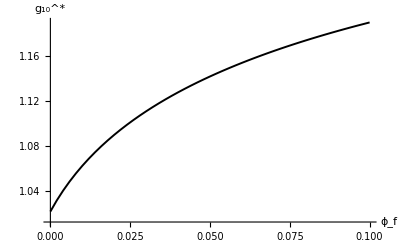

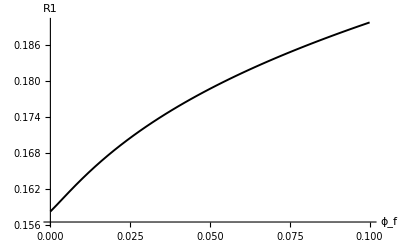

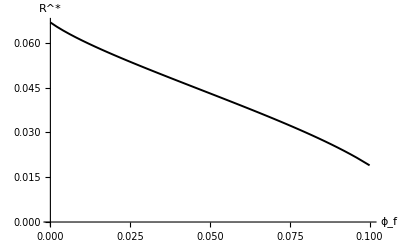

VRdataphiftestXY.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.1 XY_data\VRdataphiftestXY.xlsx

```mathematica
g1externalphif=1.18971+0.01;


RdataphiftestXY=Table[{0,0,0,0,0},{Length[vdataphiftestXY]}];
For[i=1,i<=Length[vdataphiftestXY],i++,Module[{phif,g10,n,Rstar},{phif,n,g10}=vdataphiftestXY[[i,{1,2,3}]];
R1=vdataphiftestXY[[i,4]];
Rstar=Sqrt[g1externalphif-g10]*R1;
RdataphiftestXY[[i]]={phif,g10,n,R1,Rstar};
Print[{phif,g10,n,R1,Rstar}];]];

VRdataphiftestXY=Select[RdataphiftestXY,#[[2]]>0&];
testphifnXY=ListPlot[VRdataphiftestXY[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testphifg10XY=ListPlot[VRdataphiftestXY[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifR1XY=ListLinePlot[VRdataphiftestXY[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifRXY=ListLinePlot[VRdataphiftestXY[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataphiftestXY.xlsx",VRdataphiftestXY]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdataphiftestXY.xlsx",VRdataphiftestXY]
```